## Phase Differences

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Global phase

Relative phase

Phase kickback

### Global Phase

Recall that quantum states can be represented by vectors with complex amplitudes. Strictly speaking, the geometry of this vector space is projective. That means if you multiply all amplitudes by the same complex number, this describes the same quantum state:

```mathematica
QuantumState[{a,b}]==z QuantumState[{a,b}]
```

True

A complex number multiplying all amplitudes is called a global phase. There is no known way to experimentally detect a global phase. In other words, it is a mathematical feature of quantum mechanics that has no physical effects.

However, phases can still lead to some interesting phenomena. The Z gate has a very special relationship to the states 0 and 1.

The 0 state is left completely unchanged:

```mathematica
QuantumOperator["Z"]@QuantumState["0"]//TraditionalForm
```

0

The 1 state is given a global phase, which has no physical significance by itself:

```mathematica
QuantumOperator["Z"]@QuantumState["1"]//TraditionalForm
```

-1

Does this mean that the Z gate does nothing? Consider the effect of the Z gate on a superposition state:

```mathematica
QuantumOperator["Z"][QuantumState[{a,b}]]//TraditionalForm
```

a0-b1

The Z gate introduces a relative phase between the amplitudes for 0 and 1. If you were to only measure the probabilities after applying the Z gate to this state, the distributions would look the same:

```mathematica
QuantumState[{a,b}]["Probabilities"]==QuantumOperator["Z"][QuantumState[{a,b}]]["Probabilities"]
```

True

However, the states themselves are generally not the same (except for the two special examples shown before):

```mathematica
QuantumState[{a,b}]==QuantumOperator["Z"]@QuantumState[{a,b}]//TrueQ
```

False

Relative phases between amplitudes lead to real, physical effects that can be experimentally detected.

Consider the following quantum states:

```mathematica
ψplus=QuantumState[{1/√2,1/√2},"Label"->Subscript["ψ","+"]];
ψminus=QuantumState[{1/√2,-1/√2},"Label"->Subscript["ψ","-"]];
```

Immediately measuring ψ_+ or ψ_- in the computational basis would give identical results:

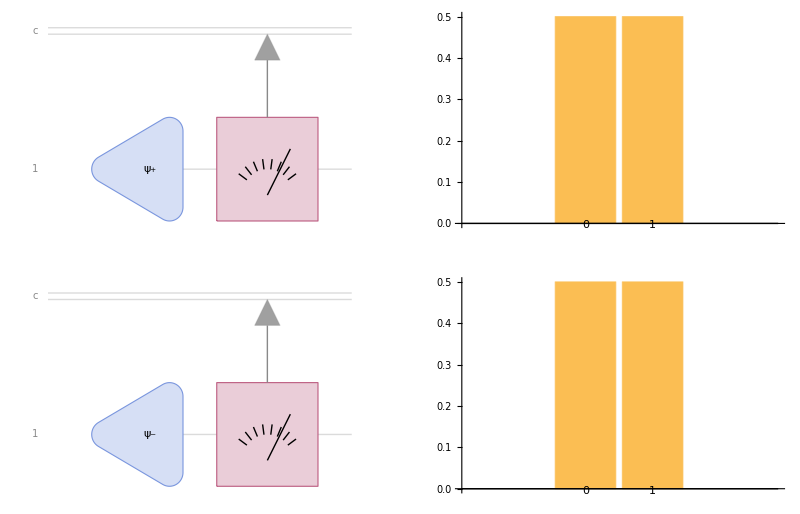

```mathematica
GraphicsGrid[
Table[
With[{qc=QuantumCircuitOperator[{state,"M"}]},
{qc["Diagram"],qc[]["ProbabilitiesPlot"]}
],{state,{ψplus,ψminus}}],
Frame->All,Dividers->{2->Directive[Dashed,LightOrange],Automatic}
]
```

However, if you first apply a Hadamard gate before measuring, you see clearly that these are not the same quantum state:

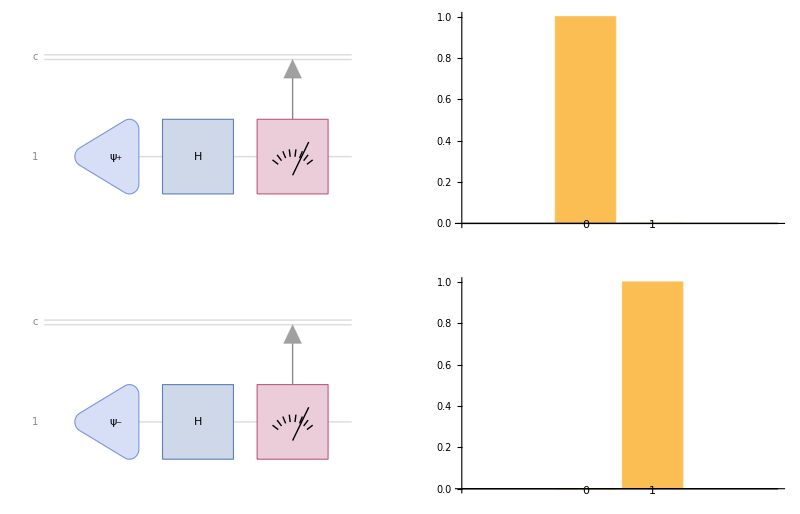

```mathematica
GraphicsGrid[
Table[
With[{qc=QuantumCircuitOperator[{state,"H","M"}]},
{qc["Diagram"],qc[]["ProbabilitiesPlot"]}
],{state,{ψplus,ψminus}}],
Frame->All,Dividers->{2->Directive[Dashed,LightOrange],Automatic}
]
```

Alternatively, you could measure not in the0/1 computational basis, but in the +/- (or “X”) basis:

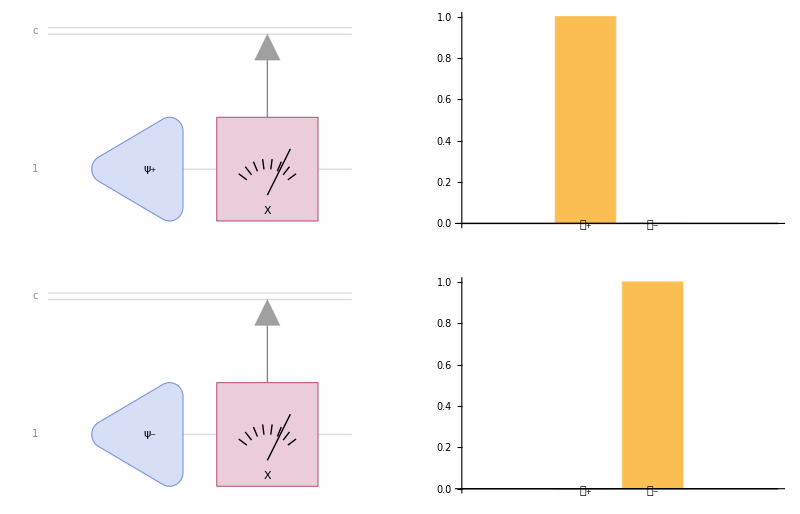

```mathematica
GraphicsGrid[
Table[
With[{qc=QuantumCircuitOperator[{state,"M"["X"]}]},
{qc["Diagram"],qc[]["ProbabilitiesPlot"]}
],{state,{ψplus,ψminus}}],
Frame->All,Dividers->{2->Directive[Dashed,LightOrange],Automatic}
]
```

These results show that while relative phases may not be detectable in every measurement basis, there is guaranteed to be some measurement which can physically distinguish states with relative phases.

The effect of relative phase in the computational basis can be detected by the following experiment:

```mathematica
ψθ=QuantumState[{1/√2,ⅇ^(ⅈ θ)1/√2},"Label"->Subscript["ψ","θ"]];
ψθ//TraditionalForm
```

1/(√2)0+ⅇ^(ⅈ θ)/(√2)1

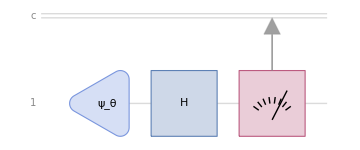

```mathematica
phasedetector=QuantumCircuitOperator[{ψθ,"H","M"}];
phasedetector["Diagram"]
```

The probabilities for this experiment have a simple dependence on the relative phase between amplitudes:

```mathematica
mprobs=phasedetector[]["Probabilities"]//Map[FullSimplify[#,θ∈Reals]&]
```

<|0→Cos[θ/2]^2,1→Sin[θ/2]^2|>

You can visualize these results as shown below:

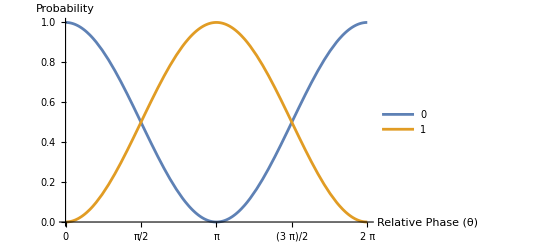

```mathematica
Plot[Evaluate@Values[mprobs],{θ,0,2Pi},
PlotLegends->Keys[mprobs],
AxesLabel->{"Relative Phase (θ)","Probability"},
PlotLabel->phasedetector["Diagram",ImageSize->Tiny],
Ticks->{Range[0,2Pi,Pi/4],Automatic}
]
```

### Phase Kickback

Previously, you conceptualized the controlled NOT gate as conditioning the state of the target qubit on the state of the control qubit. However, the phenomenon of phase kickback illustrates that the relationship between target and control qubit is not always so straightforward.

Consider the following pair of experiments. Note that only the first qubit is directly measured, but this experiment clearly gives information about the state of the second qubit:

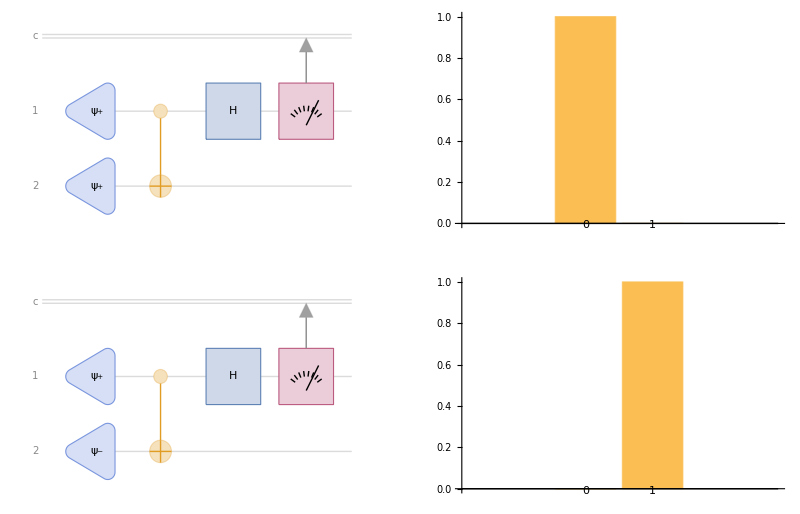

```mathematica
GraphicsGrid[
Table[
With[{qc=QuantumCircuitOperator[{ψplus->1,state->2,"CNOT"->{1,2},"H"->1,"M"->1}]},
{qc["Diagram"],qc[]["ProbabilitiesPlot"]}
],{state,{ψplus,ψminus}}],
Frame->All,Dividers->{2->Directive[Dashed,LightOrange],Automatic}
]
```

The CNOT gate “kicks back” information about the relative phase of the target qubit to the control qubit.

In fact, the experiment below gives the same result you have seen before:

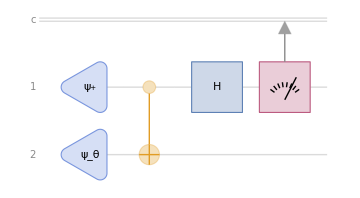

```mathematica
phasedetector2=QuantumCircuitOperator[{ψplus->1,ψθ->2,"CNOT"->{1,2},"H"->1,"M"->1}];
phasedetector2["Diagram"]
```

Even though the second qubit is never measured, the information about its relative phase has been transferred to the first qubit through the CNOT gate:

```mathematica
mprobs2=phasedetector2[]["Probabilities"]//Map[FullSimplify[#,θ∈Reals]&]
```

<|0→Cos[θ/2]^2,1→Sin[θ/2]^2|>

These results are summarized in the following plot:

```mathematica
Plot[Evaluate@Values[mprobs2],{θ,0,2Pi},
PlotLegends->Keys[mprobs2],
AxesLabel->{"Relative Phase  (θ)","Probability"},
PlotLabel->phasedetector2["Diagram",ImageSize->Small],
Ticks->{Range[0,2Pi,Pi/4],Automatic}
]
```

-Graphics-

The phenomena of phase kickback is used in several quantum algorithms.

### Control-Target Identities

The curious phenomena you have just seen also implies several interesting identities between circuits.

Consider the following two circuits:

```mathematica
qc1=QuantumCircuitOperator[{"CNOT"->{1,2}}];
qc2=QuantumCircuitOperator[{"H"->{1,2},"CNOT"->{2,1},"H"->{1,2}}];
```

Perhaps surprisingly, these two circuits are equivalent:

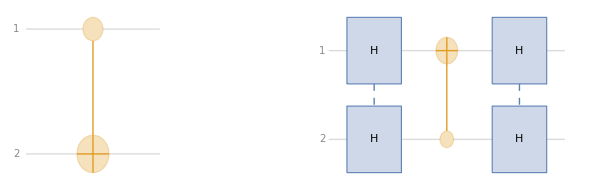

```mathematica
With[{size=150,space=40},
GraphicsRow[{qc1["Diagram",ImageSize->{Automatic,size}],Style["⟺",20,Bold],qc2["Diagram",ImageSize->{Automatic,size}]},Frame->True,Dividers->{{2->Directive[Dashed,Gray],3->Directive[Dashed,Gray]},Automatic},Spacings->{space,space}]
]
```

```mathematica
qc1==qc2
```

True

The Hadamard gates invert the relationship between the control qubit and the target qubit.

A similar relationship is true involving the controlled Z, or “CZ”, gate:

```mathematica
qc3=QuantumCircuitOperator[{"CNOT"->{2,1}}];
qc4=QuantumCircuitOperator[{"H"->1,"C"["Z"->2,1],"H"->1}];
```

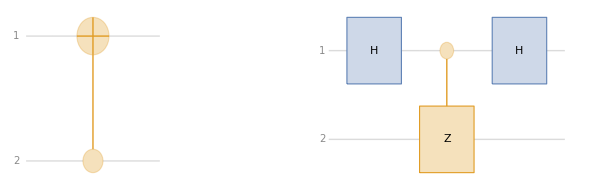

```mathematica
With[{size=150,space=40},
GraphicsRow[{qc3["Diagram",ImageSize->{Automatic,size}],Style["⟺",20,Bold],qc4["Diagram",ImageSize->{Automatic,size}]},Frame->True,Dividers->{{2->Directive[Dashed,Gray],3->Directive[Dashed,Gray]},Automatic},Spacings->{space,space}]
]
```

```mathematica
qc3==qc4
```

True

The next lesson will apply everything you have learned to quantum algorithms.